```mathematica
CellPrint[Cell["Directory","Section"]]
CellPrint[Cell["Main code & XZ independent noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"general_codes.nb"],Appearance->"DialogBox"]
CellPrint[Cell["DATA & code definitions :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depoloarizing Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Approxiating polynomials:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"approximating_polynomials.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depolarizing noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ (symmetric) noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise_ME.nb"],Appearance->"DialogBox"]
SetDirectory[NotebookDirectory[]]
```

## Directory

Main code & XZ independent noise:

DATA & code definitions :

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

XZ uneven noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

## Analysis Code

```mathematica
(*  computeMEq[] - defined in xz_noise_ME   *)
(* syndromeDistances[] - defined in xz_noise_ME *)
(* encodingPowerArray[] - defined in xz_noise_ME *)
(* encodingPowerPQArray[] - defined in xz_noise_ME *)
(* polynomialXZuneven[] - defined in *) 

computePolyMatrixXZuneven[results_,nQ_,pVal_,a_]:=Module[{polynomials,pxVal,pzVal},
polynomials = polynomialXZuneven[#,nQ]&/@#&/@results;
{pxVal,pzVal}=pxpz[a,pVal];
polynomials/.{px->pxVal,pz->pzVal}
]

computeFMatXZuneven[syndromes_,polynomials_,nQ_,p_,a_]:=Module[{fMatrix},
fMatrix=computePolyMatrixXZuneven[polynomials,nQ,p,a];
If[Plus@@Flatten@fMatrix≠1,Print[{"ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined",Plus@@Flatten@fMatrix}]];
fMatrix
]

computeMEsuccessRateXZuneven[syndromes_,polynomials_,nQ_,a_,p_,qRange_,precomputedDistance_:None]:=
Module[{fMatrix,distances,nS,nStabs,fVec},
nStabs=Length[syndromes[[1]]];
nS=Length[syndromes];
fMatrix=computeFMatXZuneven[syndromes,polynomials,nQ,p,a];


fVec=Max[#]&/@fMatrix;
distances = syndromeDistances[syndromes,nS];
computeMEq[fMatrix,distances,#,nS,nStabs]&/@qRange
(*computeMEq2[fVec,distances,#,nS,nStabs]&/@qRange*)
]

successRateArrayXZuneven[syndromes_,poly_,nQ_,a_,pRange_,qRange_]:=Module[{qR,pR,test},
pR = Table[p,{p,pRange[[1]],pRange[[2]],pRange[[3]]}];
qR=Table[q,{q,qRange[[1]],qRange[[2]],qRange[[3]]}];


test=Table[computeMEsuccessRateXZuneven[syndromes,poly,nQ,a,p,qR],{p,pRange[[1]],pRange[[2]],pRange[[3]]}];
ArrayFlatten[Table[{pR[[i]],qR[[j]],test[[i,j]]},{i,1,Length[pR]},{j,1,Length[qR]}],1]
]
```

```mathematica
CellPrint[Cell["DATA :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
```

DATA :

```mathematica
{syndromesDepolP5,polyDepolP5} =<<"data/planarDepol5.txt";
{syndromesDepolP6,polyDepolP6}=<<"data/planarDepol6.txt";
{syndromesDepolP7a,polyDepolP7a}=<<"data/planarDepol7a.txt";
{syndromesDepolP7b,polyDepolP7b}=<<"data/planarDepol7b.txt";
{syndromesDepolP8,polyDepolP8}=<<"data/planarDepol8.txt";
{syndromeDepolP9,polyDepolP9}=<<"data/planarDepol9.txt";
```

## Generate data

Evaluates data and stores to file. Cells are marked as deployed after the results have been evaluated to avoid files being overwritten.

### 5 qubit planar (for testing...)

```mathematica
successRateArrayXZuneven[syndromeXZunevenP5,polyXZunevenP5,5,2,{0.001,0.2,0.01},{0,0.01,0.001}]>>"data/xzUnevenMEP5_a2.txt"
```

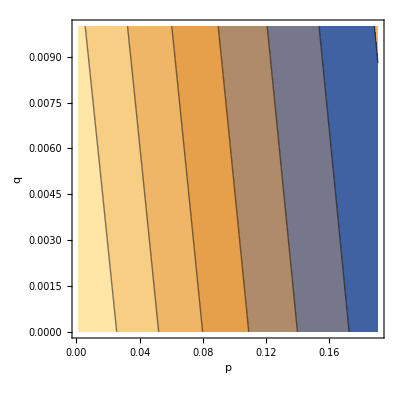
{-Graphics-,-Graphics-}

```mathematica
xzUnevenMEP5=<<"data/xzUnevenMEP5.txt";
{plotxzUnevenMEP5,plotxzUnevenMEP52}={
ListContourPlot[xzUnevenMEP5,PlotRange->{0.5,1},FrameLabel->{"p","q"}],ListContourPlot[encodingPowerPQArray[xzUnevenMEP5],PlotRange->{1,1.02},FrameLabel->{"p","q"}]}
```

### 7 qubit planar

```mathematica
{syndromeXZunevenP7,polyXZunevenP7}=<<"data/xzUnevenP7a.txt";
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP7,polyXZunevenP7,7,1,{0.001,0.1,0.005},{0,0.004,0.0005}]>>"data/xzUnevenMEP7_a1.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP7,polyXZunevenP7,7,0.5,{0.001,0.1,0.005},{0,0.004,0.0005}]>>"data/xzUnevenMEP7_a2.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP7,polyXZunevenP7,7,0.2,{0.001,0.15,0.01},{0,0.005,0.0005}]>>"data/xzUnevenMEP7_a5.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP7,polyXZunevenP7,7,0.1,{0.001,0.2,0.01},{0,0.006,0.0005}]>>"data/xzUnevenMEP7_a10.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP7,polyXZunevenP7,7,0.001,{0.001,0.2,0.01},{0,0.006,0.0005}]>>"data/xzUnevenMEP7_a1000.txt"
```

### other 7 qubit code

```mathematica
{syndromeXZunevenP7b,polyXZunevenP7b}=<<"data/xzUnevenP7b.txt";
successRateArrayXZuneven[syndromeXZunevenP7b,polyXZunevenP7b,7,0.1,{0.001,0.2,0.01},{0,0.01,0.001}]>>"data/xzUnevenMEP7a_a1.txt"
```

### 8 qubit planar

```mathematica
{syndromeXZunevenP8,polyXZunevenP8}=<<"data/xzUnevenP8.txt";
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8,polyXZunevenP8,8,1,{0.001,0.13,0.01},{0,0.0025,0.0002}]>>"data/xzUnevenMEP8_a1.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8,polyXZunevenP8,8,2,{0.001,0.15,0.01},{0,0.004,0.0005}]>>"data/xzUnevenMEP8_a2.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8,polyXZunevenP8,8,5,{0.001,0.15,0.01},{0,0.004,0.0005}]>>"data/xzUnevenMEP8_a5.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8,polyXZunevenP8,8,10,{0.001,0.15,0.01},{0,0.004,0.0005}]>>"data/xzUnevenMEP8_a10.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8,polyXZunevenP8,8,1000,{0.001,0.15,0.02},{0,0.005,0.002}]>>"data/xzUnevenMEP8_a1000.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8,polyXZunevenP8,8,1000,{0.001,0.12,0.01},{0,0.005,0.0005}]>>"data/xzUnevenMEP8_a1000.txt"
```

### 8b qubit planar

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8b,polyXZunevenP8b,8,1,{0.001,0.13,0.01},{0,0.0025,0.0002}]>>"data/xzUnevenMEP8b_a1.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8b,polyXZunevenP8b,8,0.5,{0.001,0.15,0.01},{0,0.004,0.0005}]>>"data/xzUnevenMEP8b_a2.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8b,polyXZunevenP8b,8,0.2,{0.001,0.15,0.01},{0,0.004,0.0005}]>>"data/xzUnevenMEP8b_a5.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8b,polyXZunevenP8b,8,0.1,{0.001,0.15,0.01},{0,0.004,0.0005}]>>"data/xzUnevenMEP8b_a10.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP8b,polyXZunevenP8b,8,0.001,{0.001,0.15,0.01},{0,0.004,0.0005}]>>"data/xzUnevenMEP8b_a1000.txt"
```

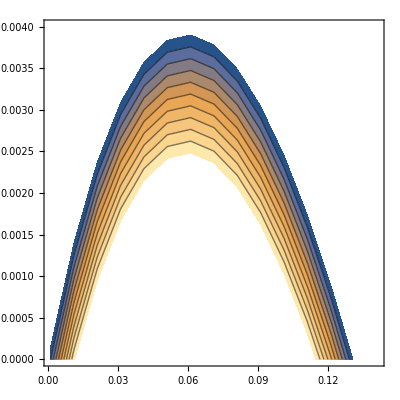

```mathematica
test=<<"data/xzUnevenMEP8b_a1000.txt";
ListContourPlot[encodingPowerArray[test],PlotRange->{1,1.01}]
```

### 9 qubit planar

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9,polyXZunevenP9,9,1,{0.001,0.2,0.01},{0,0.005,0.0005}]>>"data/xzUnevenMEP9_a1.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9,polyXZunevenP9,9,2,{0.001,0.15,0.01},{0,0.0045,0.0004}]>>"data/xzUnevenMEP9_a2.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9,polyXZunevenP9,9,5,{0.001,0.12,0.008},{0,0.0035,0.0003}]>>"data/xzUnevenMEP9_a5.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9,polyXZunevenP9,9,10,{0.001,0.1,0.005},{0,0.003,0.0003}]>>"data/xzUnevenMEP9_a10.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9,polyXZunevenP9,9,1000,{0.001,0.1,0.005},{0,0.003,0.0003}]>>"data/xzUnevenMEP9_a1000.txt"
```

### 9b qubit planar

```mathematica
{syndromeXZunevenP9b,polyXZunevenP9b} =<<"data/xzUnevenP9b.txt";
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9b,polyXZunevenP9b,9,1,{0.001,0.2,0.02},{0,0.005,0.001}]>>"data/xzUnevenMEP9b_a1.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9b,polyXZunevenP9b,9,0.5,{0.001,0.005,0.001},{0,0.0002,0.00004}]>>"data/xzUnevenMEP9b_a2.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9b,polyXZunevenP9b,9,0.2,{0.001,0.11,0.005},{0,0.002,0.0002}]>>"data/xzUnevenMEP9b_a5.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9b,polyXZunevenP9b,9,0.1,{0.001,0.15,0.007},{0,0.0035,0.0003}]>>"data/xzUnevenMEP9b_a10.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenP9b,polyXZunevenP9b,9,0.001,{0.001,0.2,0.01},{0,0.005,0.0005}]>>"data/xzUnevenMEP9b_a1000.txt"
```

### 13 qubit planar

### 7 qubit color code

```mathematica
{syndromeXZunevenC7,polyXZunevenC7} =<<"data/xzUnevenC7.txt";
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenC7,polyXZunevenC7,7,1,{0.001,0.2,0.005},{0,0.006,0.0002}]>>"data/xzUnevenMEC7_a1.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenC7,polyXZunevenC7,7,2,{0.001,0.2,0.005},{0,0.006,0.0002}]>>"data/xzUnevenMEC7_a2.txt"
```

```mathematica
successRateArrayXZuneven[syndromeXZunevenC7,polyXZunevenC7,7,5,{0.001,0.12,0.003},{0,0.004,0.0001}]>>"data/xzUnevenMEC7_a5.txt"
```

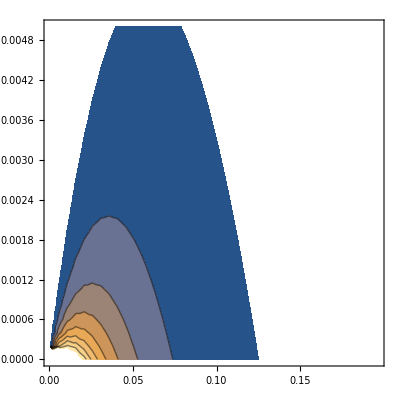

```mathematica
test=<<"data/xzUnevenMEC7_a1.txt";
ListContourPlot[correctingPowerArray[test],PlotRange->{1,5}]
```

### 11 qubit color code

```mathematica
successRateArrayDepol[syndromeDepolC11,truncatePolynomials[polyDepolC11,5],11,{0.001,0.2,0.02},{0,0.004,0.0003}]>>"data/MEdepolC11"
```

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,1.}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999998}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999982}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999909}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999688}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999159}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.998086}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.996149}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.992957}

### 13 qubit GCC

```mathematica
pGCCXZ[p_,a_]:=Module[{px,pz,nx,nz,e1x,e1z},
{px,pz}=pxpz[a,p];
nx=(1-px)^15;
nz=(1-pz)^15;
e1x=15*(1-px)^14*px;
e1z=15*(1-pz)^14*pz;
(nx+e1x)(nz+e1z)
]

qGCC[q_]:=Module[{noError,e1,e2},
noError=(1-q)^18;
e1=18*(1-q)^17*q; (* 1 error in each channel*)
e2=(36+54+3)(1-q)^16*q^2;(* 2 measurement errors on different stabilizers  *)
(noError +e1+e2)^2
]

ArrayFlatten[Table[{p,q,pGCCXZ[p,1]qGCC[q]},{p,0,0.05,0.001},{q,0,0.02,0.001}],1]>>"data/xzUnevenMEGCC15_a1.txt";
ArrayFlatten[Table[{p,q,pGCCXZ[p,2]qGCC[q]},{p,0,0.05,0.001},{q,0,0.02,0.001}],1]>>"data/xzUnevenMEGCC15_a2.txt";
ArrayFlatten[Table[{p,q,pGCCXZ[p,5]qGCC[q]},{p,0,0.05,0.001},{q,0,0.02,0.001}],1]>>"data/xzUnevenMEGCC15_a5.txt";
ArrayFlatten[Table[{p,q,pGCCXZ[p,10]qGCC[q]},{p,0,0.05,0.001},{q,0,0.02,0.001}],1]>>"data/xzUnevenMEGCC15_a10.txt";
```

## Data

```mathematica
xzUnevenMEP7a1=<<"data/xzUnevenMEP7_a1.txt";
xzUnevenMEP7a2=<<"data/xzUnevenMEP7_a2.txt";
xzUnevenMEP7a5=<<"data/xzUnevenMEP7_a5.txt";
xzUnevenMEP7a10=<<"data/xzUnevenMEP7_a10.txt";
xzUnevenMEP7a1000=<<"data/xzUnevenMEP7_a1000.txt";

xzUnevenMEP8a1=<<"data/xzUnevenMEP8_a1.txt";
xzUnevenMEP8a2=<<"data/xzUnevenMEP8_a2.txt";
xzUnevenMEP8a5=<<"data/xzUnevenMEP8_a5.txt";
xzUnevenMEP8a10=<<"data/xzUnevenMEP8_a10.txt";
xzUnevenMEP8a1000=<<"data/xzUnevenMEP8_a1000.txt";

xzUnevenMEP8ba1=<<"data/xzUnevenMEP8b_a1.txt";
xzUnevenMEP8ba2=<<"data/xzUnevenMEP8b_a2.txt";
xzUnevenMEP8ba5=<<"data/xzUnevenMEP8b_a5.txt";
xzUnevenMEP8ba10=<<"data/xzUnevenMEP8b_a10.txt";
xzUnevenMEP8ba1000=<<"data/xzUnevenMEP8b_a1000.txt";

xzUnevenMEP9a1=<<"data/xzUnevenMEP9_a1.txt";
xzUnevenMEP9a2=<<"data/xzUnevenMEP9_a2.txt";
xzUnevenMEP9a5=<<"data/xzUnevenMEP9_a5.txt";
xzUnevenMEP9a10=<<"data/xzUnevenMEP9_a10.txt";
xzUnevenMEP9a1000=<<"data/xzUnevenMEP9_a1000.txt";

xzUnevenMEP9ba5=<<"data/xzUnevenMEP9b_a5.txt";
xzUnevenMEP9ba10=<<"data/xzUnevenMEP9b_a10.txt";
xzUnevenMEP9ba1000=<<"data/xzUnevenMEP9b_a1000.txt";


xzUnevenMEC7a1=<<"data/xzUnevenMEC7_a1.txt";
xzUnevenMEC7a2=<<"data/xzUnevenMEC7_a2.txt";
xzUnevenMEC7a5=<<"data/xzUnevenMEC7_a5.txt";

xzUnevenMEGCC15a1=<<"data/xzUnevenMEGCC15_a1.txt";
xzUnevenMEGCC15a2=<<"data/xzUnevenMEGCC15_a2.txt";
xzUnevenMEGCC15a5=<<"data/xzUnevenMEGCC15_a5.txt";
xzUnevenMEGCC15a10=<<"data/xzUnevenMEGCC15_a10.txt";
```

## plots

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

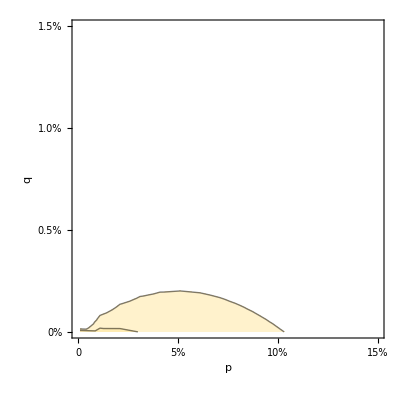
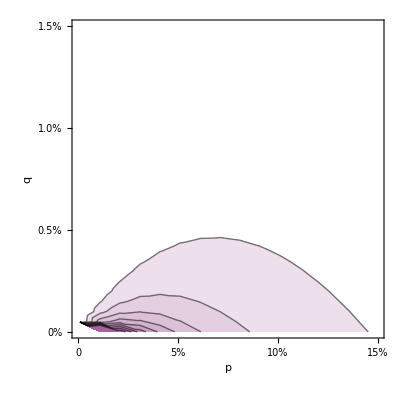
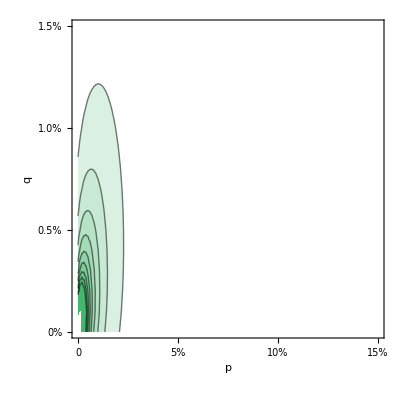
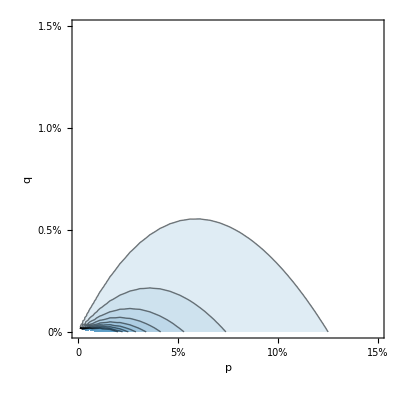
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

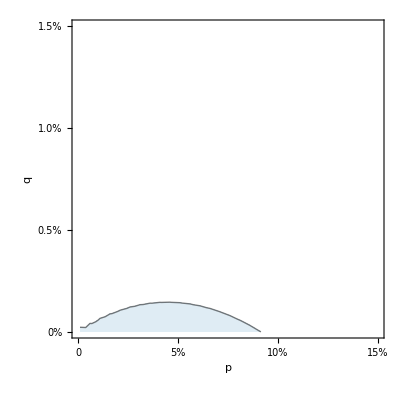
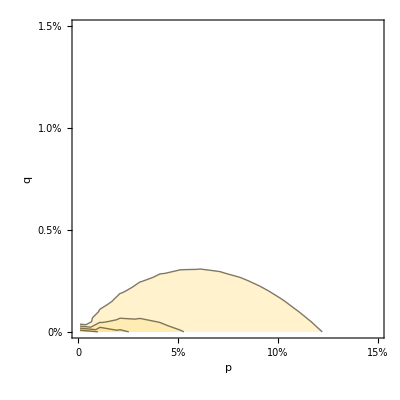
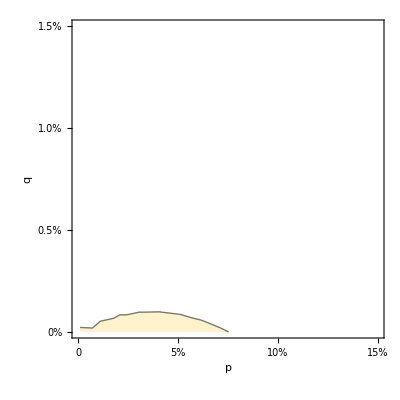
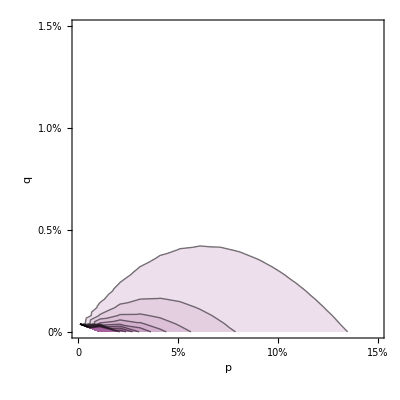
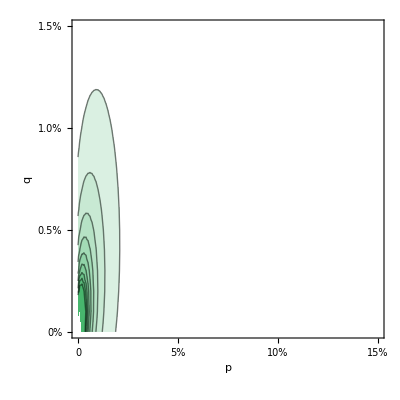
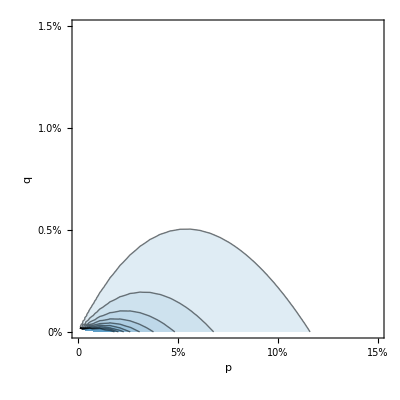

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

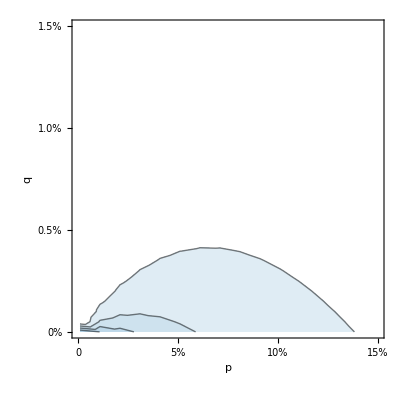
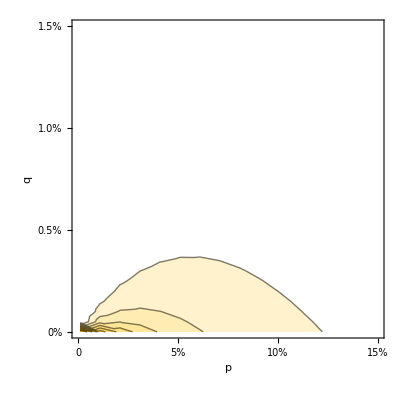
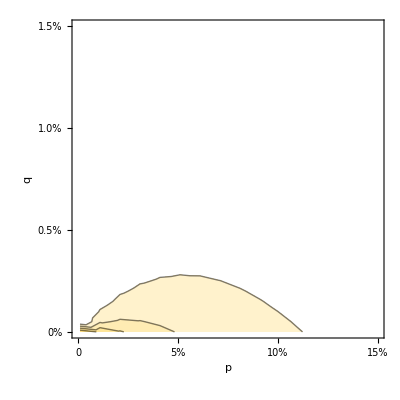
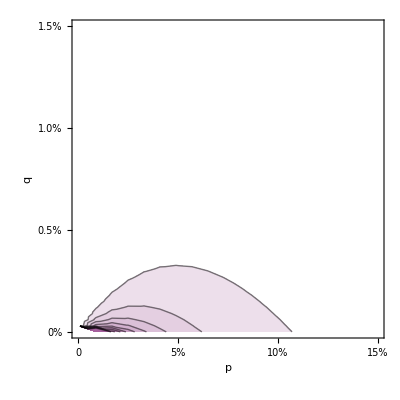
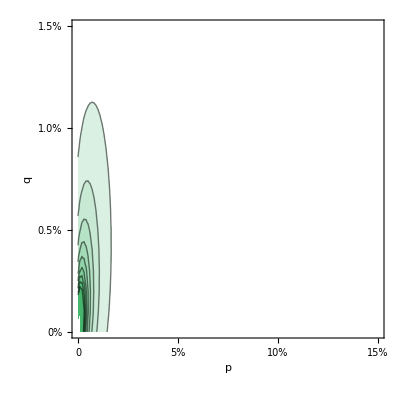
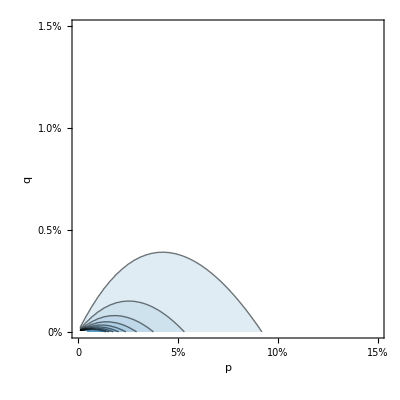

```mathematica
cp1[data_,col_]:=ListContourPlot[correctingPowerArray[data],
PlotRange->{{0,0.15},{0,0.015},{0.9999,10}},
FrameLabel->{"p","q"},
LabelStyle->20,
Contours->Range[10]*0.5,
ContourShading->Table[Blend[{White,ColorData[97,col]},x],{x,0,1,1/10}],FrameTicks->{{0,{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.005,"0.5%"},{0.01,"1.0%"},{0.015,"1.5%"}},{},{}}]

p1=cp1[#[[1]],#[[2]]]&/@{{xzUnevenMEP7a1,7},{xzUnevenMEP8a1,8},{xzUnevenMEP8ba1,8},{xzUnevenMEP9a1,9},{xzUnevenMEGCC15a1,15},{xzUnevenMEC7a1,7}}
p2=cp1[#[[1]],#[[2]]]&/@{{xzUnevenMEP7a2,7},{xzUnevenMEP8a2,8},{xzUnevenMEP8ba2,8},{xzUnevenMEP9a2,9},{xzUnevenMEGCC15a2,15},{xzUnevenMEC7a2,7}}
p5=cp1[#[[1]],#[[2]]]&/@{{xzUnevenMEP7a5,7},{xzUnevenMEP8a5,8},{xzUnevenMEP8ba5,8},{xzUnevenMEP9a5,9},{xzUnevenMEGCC15a5,15},{xzUnevenMEC7a5,7}}
```

## px=pz

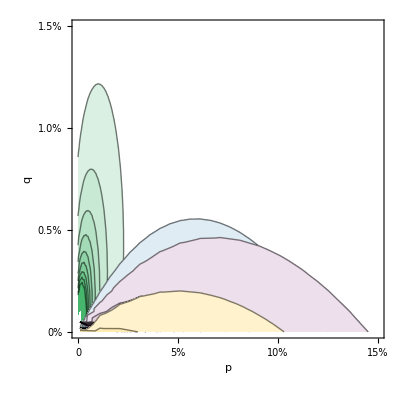

```mathematica
Show[p1[[5]],p1[[6]],p1[[4]],p1[[2]]]
```

## px=2 pz

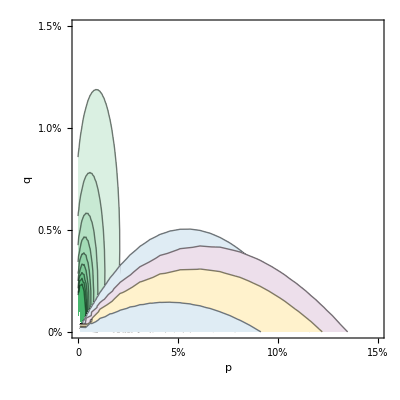

```mathematica
Show[p2[[5]],p2[[6]],p2[[4]],p2[[2]],p2[[1]]]
```

## px=5 pz

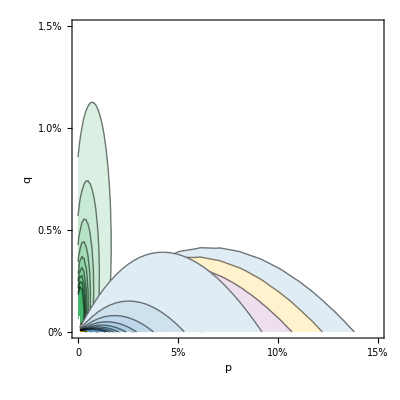

```mathematica
Show[p5[[5]],p5[[1]],p5[[2]],p5[[4]],p5[[6]]]
```